Definicje funkcji używanych przy mapowaniu:

```mathematica
GetMax[x_] :={First[x], Max[Take[x,{2,Length[x]}]]};
GetMean[x_] :={First[x], Mean[Take[x,{2,Length[x]}]]};
GetVariance[x_] :={First[x], Variance[Take[x,{2,Length[x]}]]};
GetPlusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] + StandardDeviation[Take[x,{2,Length[x]}]]};
GetMinusStandardDeviation[x_] :={First[x],Mean[Take[x,{2,Length[x]}]] - StandardDeviation[Take[x,{2,Length[x]}]]};
```

```mathematica
FLIPS :="flips"; MAX := "max_length"; MIN := "min_length"; ROUNDS := "rounds";
Problems := {FLIPS, MAX, MIN, ROUNDS};
ONE := "1"; FOUR := "4";
Leaders := {ONE, FOUR};
RawResults[p_,l_] := ReadList[StringJoin["/home/dev/Workspaces/Studies/AnalAlgo/LeaderSelection/trie_" ,p,"_",l,".m"], Number, RecordLists->True];
ResultsMax[p_,l_] := Map[GetMax, RawResults[p,l]];
ResultsMean[p_,l_] := Map[GetMean,  RawResults[p,l]];
ResultsVariance[p_,l_] := Map[GetVariance,  RawResults[p,l]];
ResultsPlusStandardDeviation[p_,l_] := Map[GetPlusStandardDeviation,  RawResults[p,l]];
ResultsMinusStandardDeviation[p_,l_] := Map[GetMinusStandardDeviation,  RawResults[p,l]];
```

Wyświetlanie wyników dla liczby rund:

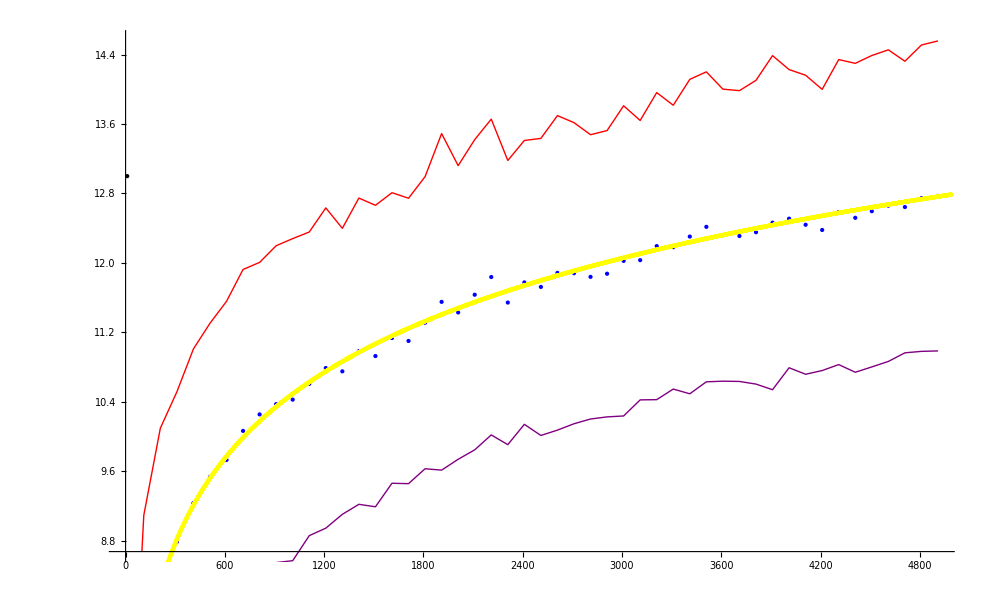

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[ROUNDS,ONE],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[ROUNDS,ONE],PlotStyle->Purple],
ListPlot[ResultsMax[ROUNDS,ONE],PlotStyle -> Black],
ListPlot[ResultsMean[ROUNDS,ONE],PlotStyle -> Blue],
ListPlot[ResultsVariance[ROUNDS,ONE], PlotStyle->Brown],
ListPlot[Table[1*Log[2,n]+0.5,{n, 10, 5000}], PlotStyle-> Yellow]
]
```

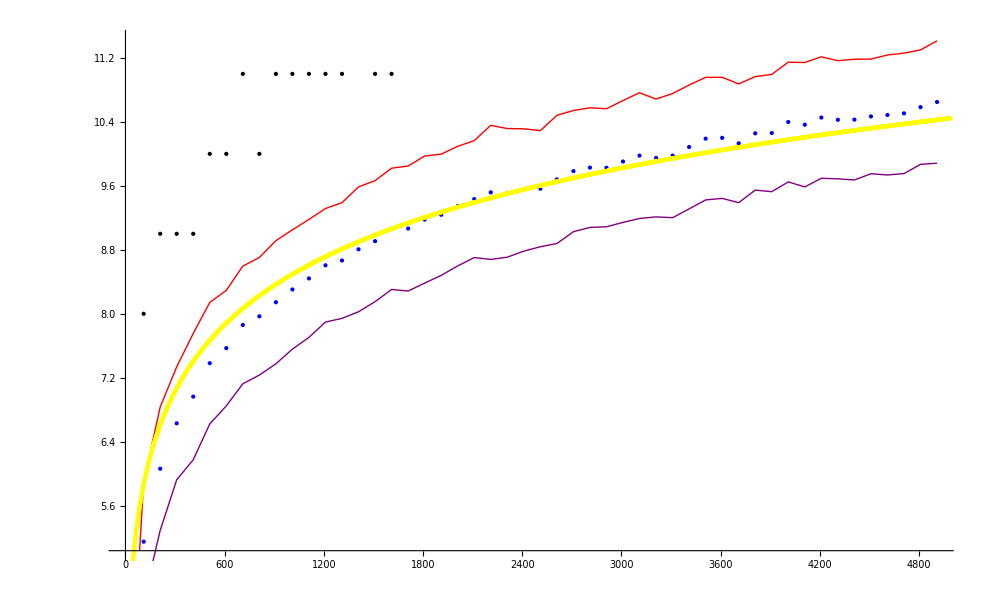

```mathematica
Show[
ListLinePlot[ResultsPlusStandardDeviation[ROUNDS,FOUR],PlotStyle->Red],
ListLinePlot[ResultsMinusStandardDeviation[ROUNDS,FOUR],PlotStyle->Purple],
ListPlot[ResultsMax[ROUNDS,FOUR],PlotStyle -> Black],
ListPlot[ResultsMean[ROUNDS,FOUR],PlotStyle -> Blue],
ListPlot[ResultsVariance[ROUNDS,FOUR], PlotStyle->Brown],
ListPlot[Table[0.85*Log[2,n],{n, 10, 5000}], PlotStyle-> Yellow]
]
```